## MOL: finite differences method

### functions

#### options settings

```mathematica
SetDirectory["mathematica/ecsf"];
ClearSystemCache[];
Needs["Splines`"];
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
```

SetDirectory::cdir: Cannot set current directory to "mathematica/ecsf".

```mathematica
SetOptions[Interpolation,InterpolationOrder->4,PeriodicInterpolation->True];
Options[Interpolation]
```

{InterpolationOrder→4,PeriodicInterpolation→True}

```mathematica
SetOptions[NIntegrate,MaxRecursion->20];
Options[NIntegrate,MaxRecursion]
```

{MaxRecursion→20}

```mathematica
SetOptions[NDSolve`FiniteDifferenceDerivative,DifferenceOrder->6,PeriodicInterpolation->True];
Options[NDSolve`FiniteDifferenceDerivative]
```

{DifferenceOrder→6,PeriodicInterpolation→True}

```mathematica
SetOptions[NDSolve,MaxSteps->15000];
Options[NDSolve,{MaxSteps,InterpolationOrder}]
```

{MaxSteps→15000,InterpolationOrder→Automatic}

```mathematica
SetOptions[NDSolve`ProcessEquations,MaxSteps->15000];
Options[NDSolve`ProcessEquations,MaxSteps]
```

{MaxSteps→15000}

#### curve generator

```mathematica
Clear[pcg,scg,sp];
pcg[num_,xy__List]:=
Module[{pts,n,spline,
fpts=50,order=8,xpts,ypts,xexp,yexp,xfk,yfk,xpara,ypara,xfitdat,yfitdat,
initialcurve,area,length,centroid},
Subscript[tf, num,0]=0;

pts=xy;
n=Length[pts];
pts=Append[pts,First[pts]];
pts=Join[{pts[[-3]],pts[[-2]]},pts,{pts[[2]],pts[[3]]}];
spline=SplineFit[pts,Cubic];

xpts=Table[{i 2π/fpts,spline[2+(n)i/fpts][[1]]},{i,0,fpts}];
ypts=Table[{i 2π/fpts,spline[2+(n)i/fpts][[2]]},{i,0,fpts}];
xexp[u_]:=Sum[Subscript[xfk, i] Cos[i u]+Subscript[xfk, order+i] Sin[i u],{i,0,order}];
yexp[u_]:=Sum[Subscript[yfk, i] Cos[i u]+Subscript[yfk, order+i] Sin[i u],{i,0,order}];
xpara=Table[Subscript[xfk, i] ,{i,0,2 order}];
ypara=Table[Subscript[yfk, i] ,{i,0,2 order}];
xfitdat=FindFit[xpts,xexp[u],xpara ,u];
yfitdat=FindFit[ypts,yexp[u],ypara ,u];
initialcurve[u_]:={xexp[u]/.xfitdat,yexp[u]/.yfitdat};

 area=1/2 
NIntegrate[Evaluate[(initialcurve[u][[2]])( D[initialcurve[u][[1]], u])-(initialcurve[u][[1]])(D[initialcurve[u][[2]], u])],{u,0,2π}
];
length=NIntegrate[Sqrt[Evaluate[(D[initialcurve[u], u]).(D[initialcurve[u], u])]],{u,0,2π}];
centroid=1/length 
NIntegrate[initialcurve[u] Sqrt[Evaluate[(D[initialcurve[u], u]).(D[initialcurve[u], u])]],{u,0,2π},AccuracyGoal->9];

Subscript[curve, num,1][u_]:=10Sqrt[2π/area](initialcurve[u]-centroid);

Print[
TableForm[{{
ParametricPlot[spline[u],{u,0,Length[pts]}],
Show[
ListPlot[xy,PlotStyle->{Red,PointSize[Medium]},AspectRatio->Full],
ListPlot[Table[spline[2+(n)i/100],{i,0,100}]],
ParametricPlot[spline[u],{u,2,2+n}]],
Show[
ListPlot[xy,PlotStyle->{Red,PointSize[Medium]},AspectRatio->Full,Axes->False],
ListPlot[Table[initialcurve[2Pi i/100],{i,0,100}]],
ParametricPlot[initialcurve[u],{u,0,2Pi}],
Graphics[{Green,PointSize[Medium],Point[centroid]}]],
Show[
ListPlot[10Sqrt[2π/area]Table[xy[[i]]-centroid,{i,1,n}],PlotStyle->{Red,PointSize[Medium]},AspectRatio->Full],
ListPlot[Table[Subscript[curve, num,1][2Pi i/100],{i,0,100}],AspectRatio->Full],
ParametricPlot[Subscript[curve, num,1][u],{u,0,2Pi}]]
}}]
];
];

scg[num_,width_,height_,kink_,touch_,asymmetrie_,diagonaldistortion_]:=
Module[{u,lo,initialcurve,
area,length,centroid},
Subscript[tf, num,0]=0;

initialcurve[u_]:=
Exp[asymmetrie (Sin[u]-1)]({width (1-kink Cos[u]^2)(Sin[u]),height  (1-touch Cos[u]^2)(Cos[u])}+diagonaldistortion{Sin[u],Sin[u]});

 area=1/2 
NIntegrate[Evaluate[(initialcurve[u][[2]])( D[initialcurve[u][[1]], u])-(initialcurve[u][[1]])(D[initialcurve[u][[2]], u])],{u,0,2π}
];
length=NIntegrate[Sqrt[Evaluate[(D[initialcurve[u], u]).(D[initialcurve[u], u])]],{u,0,2π}];
centroid=1/length 
NIntegrate[initialcurve[u] Sqrt[Evaluate[(D[initialcurve[u], u]).(D[initialcurve[u], u])]],{u,0,2π},AccuracyGoal->8];

Subscript[curve, num,1][u_]:=10Sqrt[2π/area](initialcurve[u]-centroid);
];

sp[num_,width_,height_,kink_,touch_,asymmetrie_,diagonaldistortion_]:=(
scg[num,width,height,kink,touch,asymmetrie,diagonaldistortion];
ParametricPlot[Subscript[curve, num,1][u],{u,0,2π}]);
```

#### centroid

```mathematica
Clear[centroid,centab];
centroid[num_,step_]:=
Module[{x,y,area,length,cen},
x=Subscript[curve, num,step][u][[1]];
y=Subscript[curve, num,step][u][[2]];

area=1/2 
NIntegrate[Evaluate[(x)( D[y, u])-(y)(D[x, u])],{u,0,2π}
];
length=NIntegrate[Sqrt[Evaluate[(D[x, u])^2+(D[y, u])^2]],{u,0,2π}];
cen=1/length NIntegrate[Evaluate[{x,y}  Sqrt[(D[x, u])^2+(D[y, u])^2]],{u,0,2π},AccuracyGoal->8,MaxRecursion->20]
];

centab[num_]:=Table[centroid[num,i],{i,1,Subscript[steps, num]}]
```

#### method of lines

```mathematica
Clear[flow,fp];
flow[num_,step_,dt_,grid_:150,opts___]:=Module[{n=grid,grdpts,ugrid,t1,t2,X,Y,xu,yu,xuu,yuu,v,xeqns,yeqns,xic,yic,xicval,yicval},

grdpts=Range[0,n];
ugrid=2π/n grdpts;
t1=Subscript[tf, num,step-1];
t2=Subscript[tf, num,step]=t1+dt;

X[t_]=Through[Thread[Subscript[x, grdpts]][t]];
Y[t_]=Through[Thread[Subscript[y, grdpts]][t]];

xu=NDSolve`FiniteDifferenceDerivative[Derivative[1],ugrid,X[t]];
yu=NDSolve`FiniteDifferenceDerivative[Derivative[1],ugrid,Y[t]];
xuu=NDSolve`FiniteDifferenceDerivative[Derivative[2],ugrid,X[t]];
yuu=NDSolve`FiniteDifferenceDerivative[Derivative[2],ugrid,Y[t]];
v=Table[Sqrt[(xu[[i]])^2+(yu[[i]])^2],{i,1,n+1}];

xeqns = Thread[D[X[t], t] ==v^(-2)(-v^(-2)(xu xuu +yu yuu)xu+xuu)];
yeqns = Thread[D[Y[t], t] ==v^(-2)(-v^(-2)(xu xuu +yu yuu)yu+yuu)];

xic=Thread[X[t1]==Subscript[curve, num,step][u][[1]]/.u->ugrid];
yic=Thread[Y[t1]==Subscript[curve, num,step][u][[2]]/.u->ugrid];

Subscript[sol, num,step]=
NDSolve[
Join[xeqns,yeqns,xic,yic],Join[Table[Subscript[x, i],{i,0,n}],
Table[Subscript[y, i],{i,0,n}]],
{t,t1,t2},
opts
];

If[step==1,Subscript[gpn, num,1]=grid;Subscript[dmin, num]=Min[Table[dist[num,1,0,i,i-1],{i,1,grid}]],None,Print["Error bei gpn Zuweisung und dmin Ermittelung"]
];

];

fp[num_,step_,dt_,grid___,opts___]:=
Module[{plot,time},
time=Timing[flow[num,step,dt,grid,opts];][[1]];
Print[
"grid points: ",Subscript[gpn, num,step],
", minimum distance at t=0: ", Subscript[dmin, num],
", evaluation time: ",time
];
plot3d[num,step]
];
```

#### plotting

```mathematica
Clear[plot3d,plot,evoplot,dplot,fplot];
plot3d[num_,step_,stretch_:1]:=
Module[{plots,n=Subscript[gpn, num,step],t1=Subscript[tf, num,step-1],t2=Subscript[tf, num,step]},
plots=Table[{stretch Subscript[x, i][t]/.Subscript[sol, num,step][[1,i+1]],stretch Subscript[y, i][t]/.Subscript[sol, num,step][[1,i+n+2]],t},{i,0,n}
];
ParametricPlot3D[plots//Evaluate,{t,t1,t2},AspectRatio->1,PerformanceGoal->"Speed"]
];

plot[num_,step_,t_,intord_:6]:=
Module[{xint,yint,tt=t,n=Subscript[gpn, num,step]},
xint=Interpolation[
Evaluate[Table[{2π i/n,Subscript[x, i][tt]/.Subscript[sol, num,step][[1,i+1]]},{i,0,n}]],InterpolationOrder->intord
];
yint=Interpolation[
Evaluate[Table[{2π i/n,Subscript[y, i][tt]/.Subscript[sol, num,step][[1,i+n+2]]},{i,0,n}]],InterpolationOrder->intord
];
ParametricPlot[{xint[u],yint[u]},{u,0,2π},PerformanceGoal->"Speed"]
];

evoplot[num_,opts___]:=Block[{n=Subscript[steps, num],stretch=3},
Show[
ParametricPlot3D[
{{stretch Subscript[curve, num,1][u][[1]],stretch Subscript[curve, num,1][u][[2]],0},{0,0,Subscript[tf, num,n]}},
{u,0,2π},PlotRange->All,PerformanceGoal->"Speed",opts],
Table[
plot3d[num,i,stretch],{i,1,n}]
]
];

dplot[num_,comp_:1]:=Show[Plot[Evaluate[{D[Subscript[curve, num,0][u][[comp]], u],D[Subscript[curve, num,0][u][[comp]], u,u],,2 D[Subscript[curve, num,0][u][[comp]], u,u,u]}],{u,0,2π}]];

fplot[nn_]:=
Show[Plot[{lt[nn,t]^2/at[nn,t],Subscript[iso, nn][t],4π},{t,0,99},PerformanceGoal->"Speed",PlotRange->All],ListPlot[lla[nn]]];
```

#### length & area

```mathematica
Clear[clength,carea,les,ars,cus,cus2];
clength[num_,step_,opts___]:=Module[{c=D[Subscript[curve, num,step][u], u]},
NIntegrate[Sqrt[Evaluate[(c).(c)]],{u,0,2π},opts]];

carea[num_,step_,opts___]:= Module[{c=Subscript[curve, num,step][u]},NIntegrate[(c[[2]])( D[c[[1]], u])-(c[[1]])(D[c[[2]], u]),{u,0,2π},opts]/2];

ars[num_,step_,t_]:=
Block[{n=Subscript[gpn, num,step],grid,x,y,tt,fddf},

grid=Range[1,n];
x=Through[Thread[Subscript[x, grid]][t]]/.Subscript[sol, num,step][[1]];
y=Through[Thread[Subscript[y, grid]][t]]/.Subscript[sol, num,step][[1]];
fddf = NDSolve`FiniteDifferenceDerivative[Derivative[1], Range[0,n]];

Abs[
Total[fddf[x] y -fddf[y]x]/2
]
];

les[num_,step_,t_]:=
Block[{n=Subscript[gpn, num,step],grid,x,y,tt,fddf},

grid=Range[1,n];
x=Through[Thread[Subscript[x, grid]][t]]/.Subscript[sol, num,step][[1]];
y=Through[Thread[Subscript[y, grid]][t]]/.Subscript[sol, num,step][[1]];
fddf = NDSolve`FiniteDifferenceDerivative[Derivative[1], Range[0,n]];

Total[Sqrt[fddf[x]^2 +fddf[y]^2]]

];

cus[num_,step_,t_]:=
Block[{n=Subscript[gpn, num,step],grid,x,y,tt,fddf,fddf2},

grid=Range[1,n];
x=Through[Thread[Subscript[x, grid]][t]]/.Subscript[sol, num,step][[1]];
y=Through[Thread[Subscript[y, grid]][t]]/.Subscript[sol, num,step][[1]];
fddf = NDSolve`FiniteDifferenceDerivative[Derivative[1], Range[0,n]];
fddf2 = NDSolve`FiniteDifferenceDerivative[Derivative[2], Range[0,n]];

Abs[Total[(fddf[x] fddf2[y] -fddf[y]fddf2[x])(fddf[x]^2+fddf[y]^2)^(-1)]]

];

cus2[num_,step_,t_]:=
Block[{n=Subscript[gpn, num,step],grid,x,y,tt,fddf,fddf2},

grid=Range[1,n];
x=Through[Thread[Subscript[x, grid]][t]]/.Subscript[sol, num,step][[1]];
y=Through[Thread[Subscript[y, grid]][t]]/.Subscript[sol, num,step][[1]];
fddf = NDSolve`FiniteDifferenceDerivative[Derivative[1], Range[0,n]];
fddf2 = NDSolve`FiniteDifferenceDerivative[Derivative[2], Range[0,n]];

Total[((fddf[x] fddf2[y] -fddf[y]fddf2[x])(fddf[x]^2+fddf[y]^2)^(-5/2))^2]

];
```

#### point distance

```mathematica
Clear[dist];
dist[num_,step_,t_,i_,j_]:=Sqrt[((Subscript[x, i][t]/.Subscript[sol, num,step][[1,i+1]])-(Subscript[x, j][t]/.Subscript[sol, num,step][[1,j+1]]))^2+((Subscript[y, i][t]/.Subscript[sol, num,step][[1,i+Subscript[gpn, num,step]+2]])-(Subscript[y, j][t]/.Subscript[sol, num,step][[1,j+Subscript[gpn, num,step]+2]]))^2];
```

#### fit

```mathematica
Clear[fit];
fit[num_,step_,t_]:=Module[{n,dm,d,i,j,mdp,lmdp,l,ll,umdp,xmdp,ymdp,order,xexp,yexp,xfk,yfk,xpara,ypara,yfitdat,xfitdat},
n=Subscript[gpn, num,step];
dm=Subscript[dmin, num];
mdp=
Reap[
For[
{i=1;j=0},
i≤ n,
i++,
d=dist[num,step,t,i,j];
If[
d≥ dm,
{Sow[{d,i}];j=i},None,Print["Error at mdp"]
]
]
][[2,1]];
lmdp=Length[mdp];
Subscript[l, 0]=0;
Do[Subscript[l, i]=Subscript[l, i-1]+mdp[[i,1]],{i,1,lmdp}];
ll=Subscript[l, lmdp];
mdp=Prepend[mdp,{0,0}];

xmdp=Table[{2π Subscript[l, i]/ll,Subscript[x, mdp[[i+1,2]]][t]/.Subscript[sol, num,step][[1,mdp[[i+1,2]]+1]]},{i,0,lmdp}];
ymdp=Table[{2π Subscript[l, i]/ll,Subscript[y, mdp[[i+1,2]]][t]/.Subscript[sol, num,step][[1,n+mdp[[i+1,2]]+2]]},{i,0,lmdp}];

order=16-IntegerPart[t/8];
xexp[u_]:=Sum[Subscript[xfk, i] Cos[i u]+Subscript[xfk, order+i] Sin[i u],{i,0,order}];
yexp[u_]:=Sum[Subscript[yfk, i] Cos[i u]+Subscript[yfk, order+i] Sin[i u],{i,0,order}];
xpara=Table[Subscript[xfk, i] ,{i,0,2 order}];
ypara=Table[Subscript[yfk, i] ,{i,0,2 order}];
xfitdat=FindFit[xmdp,xexp[u],xpara ,u];
yfitdat=FindFit[ymdp,yexp[u],ypara ,u];

Subscript[curve, num,step+1][u_]:={xexp[u]/.xfitdat,yexp[u]/.yfitdat};

Subscript[gpn, num,step+1]=lmdp
];

fip[num_,step_,t_,order___]:=
(
fit[num,step,t,order];
Show[
ParametricPlot[Subscript[curve, num,step+1][u],{u,0,2π}],
ListPlot[Table[Subscript[curve, num,step+1][2π/Subscript[gpn, num,step+1]i],{i,0,Subscript[gpn, num,step+1]}],PlotStyle->{Red}]
]
)
```

#### errorfunction

```mathematica
Clear[erf,erf2];
erf2[num_,step_,t_]:=
Block[{n=Subscript[gpn, num,step],grid,x,y,tt,fddf},

grid=Range[1,n];
x=Through[Thread[Subscript[x, grid]][t]]/.Subscript[sol, num,step][[1]];
y=Through[Thread[Subscript[y, grid]][t]]/.Subscript[sol, num,step][[1]];
fddf = NDSolve`FiniteDifferenceDerivative[Derivative[1], Range[0,n]];

1000Abs[
Total[fddf[x] y -fddf[y]x]/2+2π t -200π
]
];

erf[num_,step_,t_]:=1000Abs[carea[num,step]+2π Subscript[tf, num,step-1]-(ars[num,step,t]+2π t)]
```

#### process equation

```mathematica
Clear[staf];
staf[num_,step_,n_:150,t0_:0]:=Module[{grdpts,ugrid,X,Y,xu,xuu,yu,yuu,v,xeqns,yeqns,xic,yic},

grdpts=Range[0,n];
ugrid=2π/n grdpts;

X[t_]=Through[Thread[Subscript[x, grdpts]][t]];
Y[t_]=Through[Thread[Subscript[y, grdpts]][t]];

xu=NDSolve`FiniteDifferenceDerivative[Derivative[1],ugrid,X[t]];
yu=NDSolve`FiniteDifferenceDerivative[Derivative[1],ugrid,Y[t]];
xuu=NDSolve`FiniteDifferenceDerivative[Derivative[2],ugrid,X[t]];
yuu=NDSolve`FiniteDifferenceDerivative[Derivative[2],ugrid,Y[t]];
v=Table[Sqrt[(xu[[i]])^2+(yu[[i]])^2],{i,1,n+1}];

xeqns = Thread[D[X[t], t] ==v^(-2)(-v^(-2)(xu xuu +yu yuu)xu+xuu)];
yeqns = Thread[D[Y[t], t] ==v^(-2)(-v^(-2)(xu xuu +yu yuu)yu+yuu)];

xic=Thread[X[t0]==Subscript[curve, num,step][u][[1]]/.u->ugrid];
yic=Thread[Y[t0]==Subscript[curve, num,step][u][[2]]/.u->ugrid];

First[
NDSolve`ProcessEquations[
Join[xeqns,yeqns,xic,yic],
Join[Thread[Subscript[x, grdpts]],Thread[Subscript[y, grdpts]]],
t]
]
];
```

#### iteration and solution processing

```mathematica
Clear[itf];
itf[num_,step_,n_,t1_]:=Module[{state,t,t2,a,d},
Subscript[gpn, num,step]=n;
state=staf[num,step,n,t1];
t2=Catch[
For[t=t1,t≤100  ,t++,
If[t==100,t=99+ars[num,step,99]/2/π];
NDSolve`Iterate[state, t];
Subscript[sol, num,step] = {NDSolve`ProcessSolutions[state]};
If[step==1,
Subscript[dmin, num]=Min[Table[dist[num,1,0,i,i-1],{i,1,n}]];
];
If[t>99,Throw[t];Break[]];
d=erf[num,step,t];
If[d≥ 1,Print["Fit at t = ",t,", erf = ", d];Throw[t];,None,Print["Error at exit function, error = ",d,", t = ",t];Throw[t];
];
];
];
Subscript[tf, num,step]=t2
];
```

#### evolution

```mathematica
Clear[evo];
evo[num_,grd_:150]:=Module[{step,t=0,grid=grd},
For[step=1,t<100,step++,
t=itf[num,step,grid,t];
If[t>99,Break[]];
grid=fit[num,step,t];
];
Subscript[steps, num]=step;
Print[num,". curve, T - 100 = ",t-100,", steps = ",step];
]
```

#### invariant error plot

```mathematica
Clear[invar];
invar[num_,step_,n_,t1_,t2_,opts___]:=Module[{t,state,fsol,vv,vars,grid,XX,YY,xu,yu,invariant},
state=staf[num,step,n,t1,opts];
NDSolve`Iterate[state,t2];
fsol={NDSolve`ProcessSolutions[state]};
vv=state@"DependentVariables";
vars=Through[vv[t]];

grid=Range[0,n];
XX[t_]=Through[Thread[Subscript[x, grid]][t]];
YY[t_]=Through[Thread[Subscript[y, grid]][t]];
xu=NDSolve`FiniteDifferenceDerivative[Derivative[1],grid,XX[t],DifferenceOrder->6];
yu=NDSolve`FiniteDifferenceDerivative[Derivative[1],grid,YY[t],DifferenceOrder->6];
invariant=1000(Sum[YY[t][[i]] xu[[i]]-XX[t][[i]] yu[[i]],{i,1,n}]/2+2π t-200π);

InvariantErrorPlot[invariant,vars,t,fsol]
]
```

#### total functions: length, area, iso

```mathematica
Clear[lt,at,cut,lla,llafit,l];
lt[num_,t_]:=
Module[{i,l},
For[i=1,i≤Subscript[steps, num],i++,
If[Subscript[tf, num,i-1]≤ t ≤ Subscript[tf, num,i],Break[]
]
];
les[num,i,t]
];

at[num_,t_]:=
Module[{i,l},
For[i=1,i≤Subscript[steps, num],i++,
If[Subscript[tf, num,i-1]≤ t ≤ Subscript[tf, num,i],Break[]
]
];
ars[num,i,t]
];

cut[num_,t_]:=
Module[{i,l},
For[i=1,i≤Subscript[steps, num],i++,
If[Subscript[tf, num,i-1]≤ t ≤ Subscript[tf, num,i],Break[]
]
];
cus[num,i,t]
];

cut2[num_,t_]:=
Module[{i,l},
For[i=1,i≤Subscript[steps, num],i++,
If[Subscript[tf, num,i-1]≤ t ≤ Subscript[tf, num,i],Break[]
]
];
cus2[num,i,t]
];

lla[num_]:=
Append[Table[{t,lt[num,t]^2/at[num,t]},{t,0,99}],{100,4π}];

llafit[num_,order_:20]:=Fit[lla[num],Thread[t^Range[0,order]],t];

Subscript[l, num_][t_]:=Sqrt[Subscript[iso, num][t](200π-2π t)]
```

#### c(t) fit

```mathematica
ccfit[noc_,t1_,t2_,pts_:50]:=Block[{data,expr,pars},
data=Table[{t1 +(t2-t1)i/pts,(c[t1 +(t2-t1)i/pts]/.Subscript[zsol, noc][[1]])^2},{i,0,pts}];
expr=k Abs[(100-t)]^v;
pars={{k,400},{v,1}};
Subscript[cf, noc]=FindFit[data,expr,pars,t];
{Sqrt[k],v/2}/. Subscript[cf, noc]
]
```

### evolution

#### specific & random curves

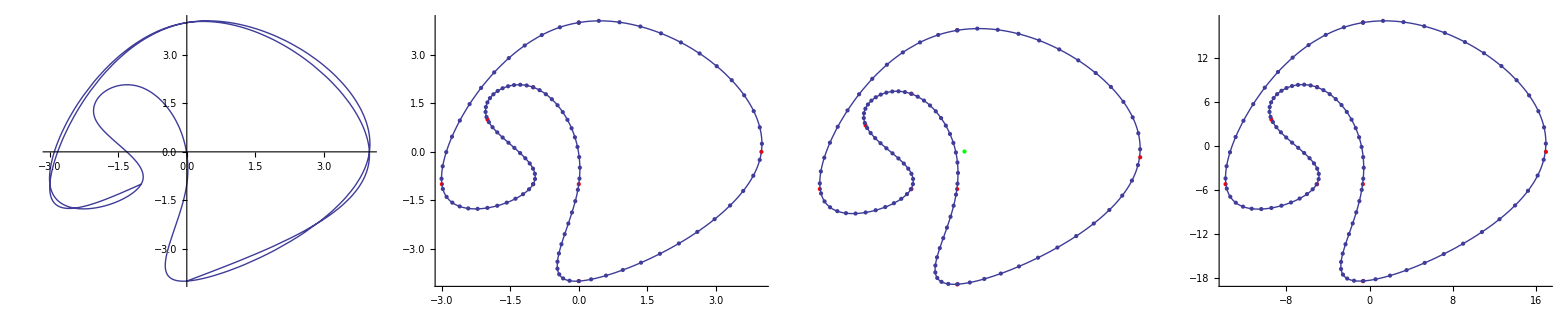

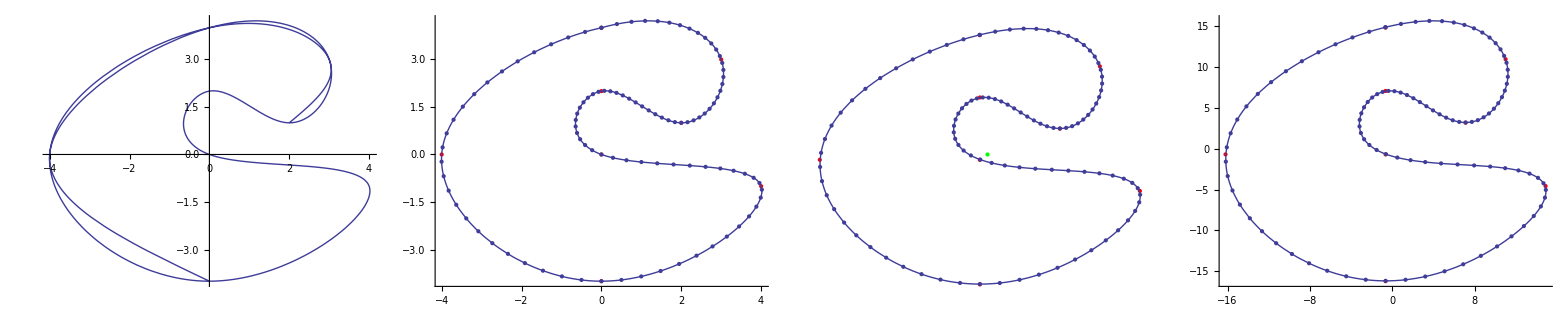

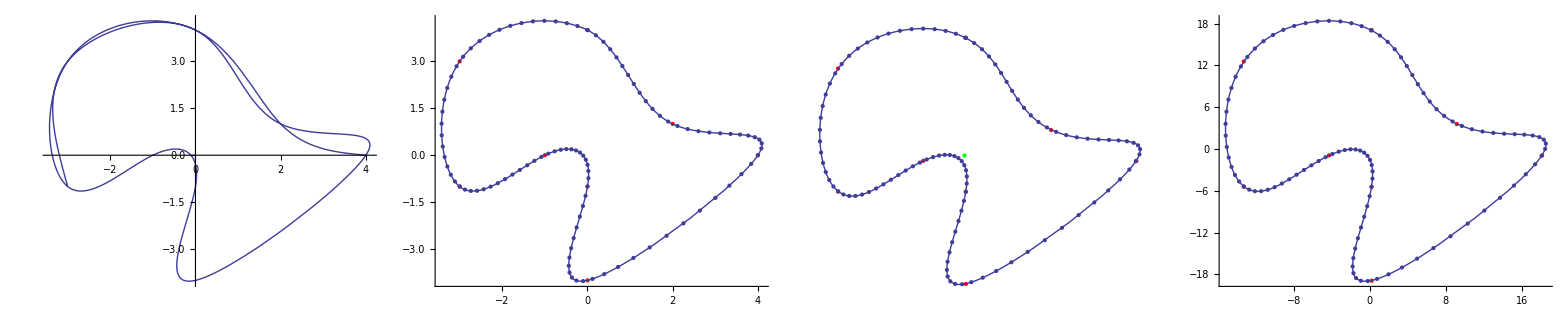

```mathematica
sp[0, 1, 1,0,0 ,0,0];
pcg[1,{{0,4},{4,0},{0,-4},{0,-1},{-1,2},{-2,1},{-1,-1},{-3,-1}}];
pcg[2,{{0,4},{3,3},{2,1},{0,2},{0,0},{4,-1},{0,-4},{-4,0}}];
sp[3, 165/100, 5/10,1,0 ,0,-6/10];
sp[4,1,15/10,-2,0,0,-6/10];
sp[5,3/2, 1/2,1,1/2 ,1/6,1/2];
sp[6,2,1,-1,-1,-1,-3/4];
sp[7,1,1,-25/10,-1/2,-1/2,1/5];
sp[8,1,1,4/10,9/10,5/10,0];
sp[9,1,1,4/10,9/10,0,0];
sp[10,1,1,4/10,8/10,3/10,4/10];
sp[11,1,1,4/10,8/10,3/10,-4/10];
sp[12,1,1,7/10,99/100,0,0];
sp[13,1,1,-2,-1/2,-3/5,1/2];
sp[14,5,1,0,0,0,0];
sp[15,1,1,1/2,-1/2,2,1/2];
sp[16, 1, 1,8/10,0 ,0,1/7];
pcg[17,{{0,4},{2,1},{4,0},{0,-4},{0,-1},{-1,0},{-3,-1},{-3,3}}];
```

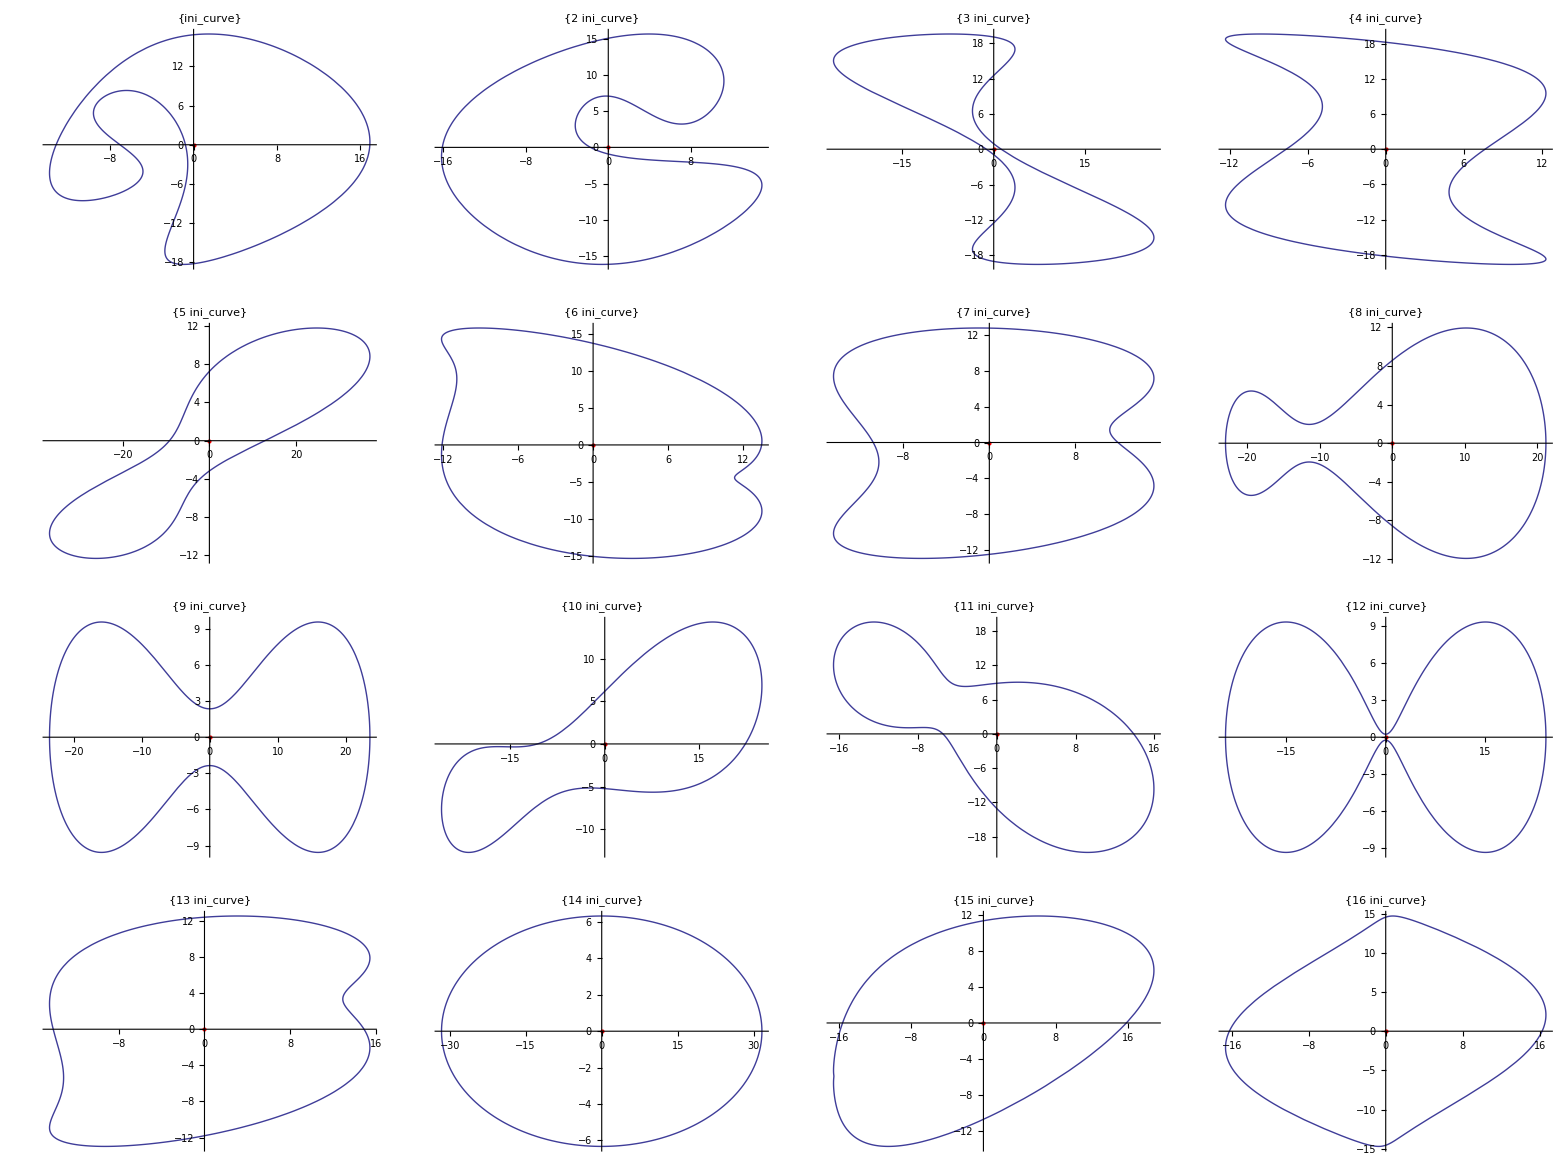

```mathematica
Print[iniplots=TableForm[Table[Table[
Show[
ParametricPlot[Subscript[curve, 4j+ i,1][u],{u,0,2π},AspectRatio->Full,PlotLabel->{(4j+ i)"ini_curve"}],
Graphics[{Red,PointSize[Large],Point[centroid[4j+ i,1]]}]
],{i,1,4}],{j,0,3}]
]
];
Export["ini_plots.gif",iniplots];
```

#### evolution

```mathematica
Timing[evo[1]]
```

Fit at t = 15, erf = 1.14153

Fit at t = 18, erf = 1.52776

Fit at t = 22, erf = 1.57969

Fit at t = 41, erf = 1.05038

1. curve, T - 100 = 0.00684562, steps = 5

{21.3613,Null}

```mathematica
evo[2]
```

Fit at t = 89, erf = 1.00821

2. curve, T - 100 = -0.000163512, steps = 2

```mathematica
evo[17]
```

Fit at t = 1, erf = 1.71125

Fit at t = 3, erf = 1.77962

Fit at t = 12, erf = 1.01169

17. curve, T - 100 = 0.0351158, steps = 4

```mathematica
evoplot[1]
```

-Graphics3D-

```mathematica
TableForm[{{evoplot[1],evoplot[2],evoplot[17]}}]
```

-Graphics3D- | -Graphics3D- | -Graphics3D-

```mathematica
evo[11]
```

Fit at t = 93, erf = 1.58615

11. curve, T - 100 = 0.000637708, steps = 2

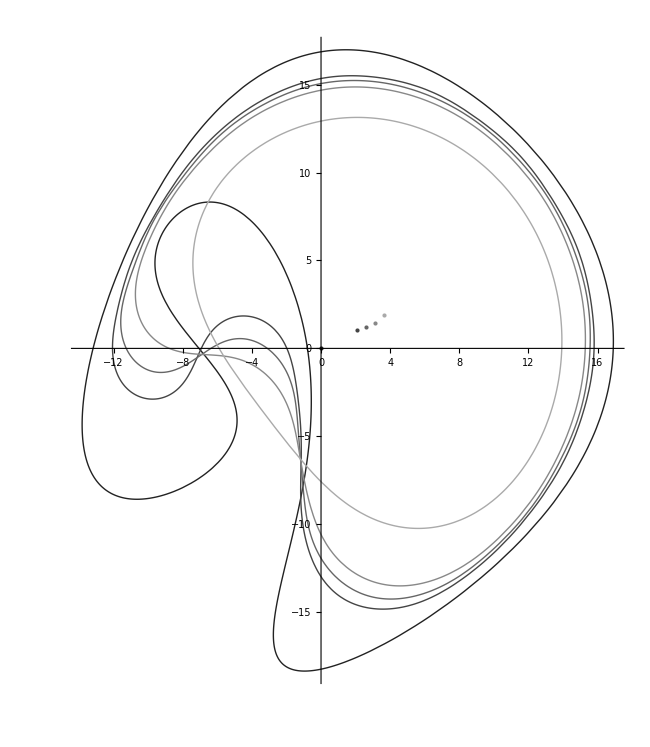

```mathematica
Block[{num=1},
Show[
Table[{
ParametricPlot[Subscript[curve, num,i][u],{u,0,2Pi},
PlotStyle->GrayLevel[i/(Subscript[steps, num])2/3]
],
Graphics[{GrayLevel[i/(Subscript[steps, num])2/3],PointSize[Medium],Point[centroid[num,i]]}]}
,{i,1,Subscript[steps, num]}
]
]
]
```

#### invariants

```mathematica
l2a[num_]:=Plot[lt[num,t] ^2/at[num,t],{t,0,99.5},PerformanceGoal->"Speed",PlotRange->All]
```

```mathematica
lc[num_]:=Plot[lt[num,t] cut[num,t],{t,0,99.5},PerformanceGoal->"Speed",PlotRange->All]
```

```mathematica
l2c[num_]:=Plot[lt[num,t]^2 cut2[num,t],{t,0,99.5},PerformanceGoal->"Speed",PlotRange->All]
```

```mathematica
acc[num_]:=Plot[at[num,t] cut2[num,t],{t,0,99.5},PerformanceGoal->"Speed",PlotRange->All]
```

```mathematica
a12c[num_]:=Plot[at[num,t]^(1/2) cut[num,t],{t,0,99.5},PerformanceGoal->"Speed",PlotRange->All]
```

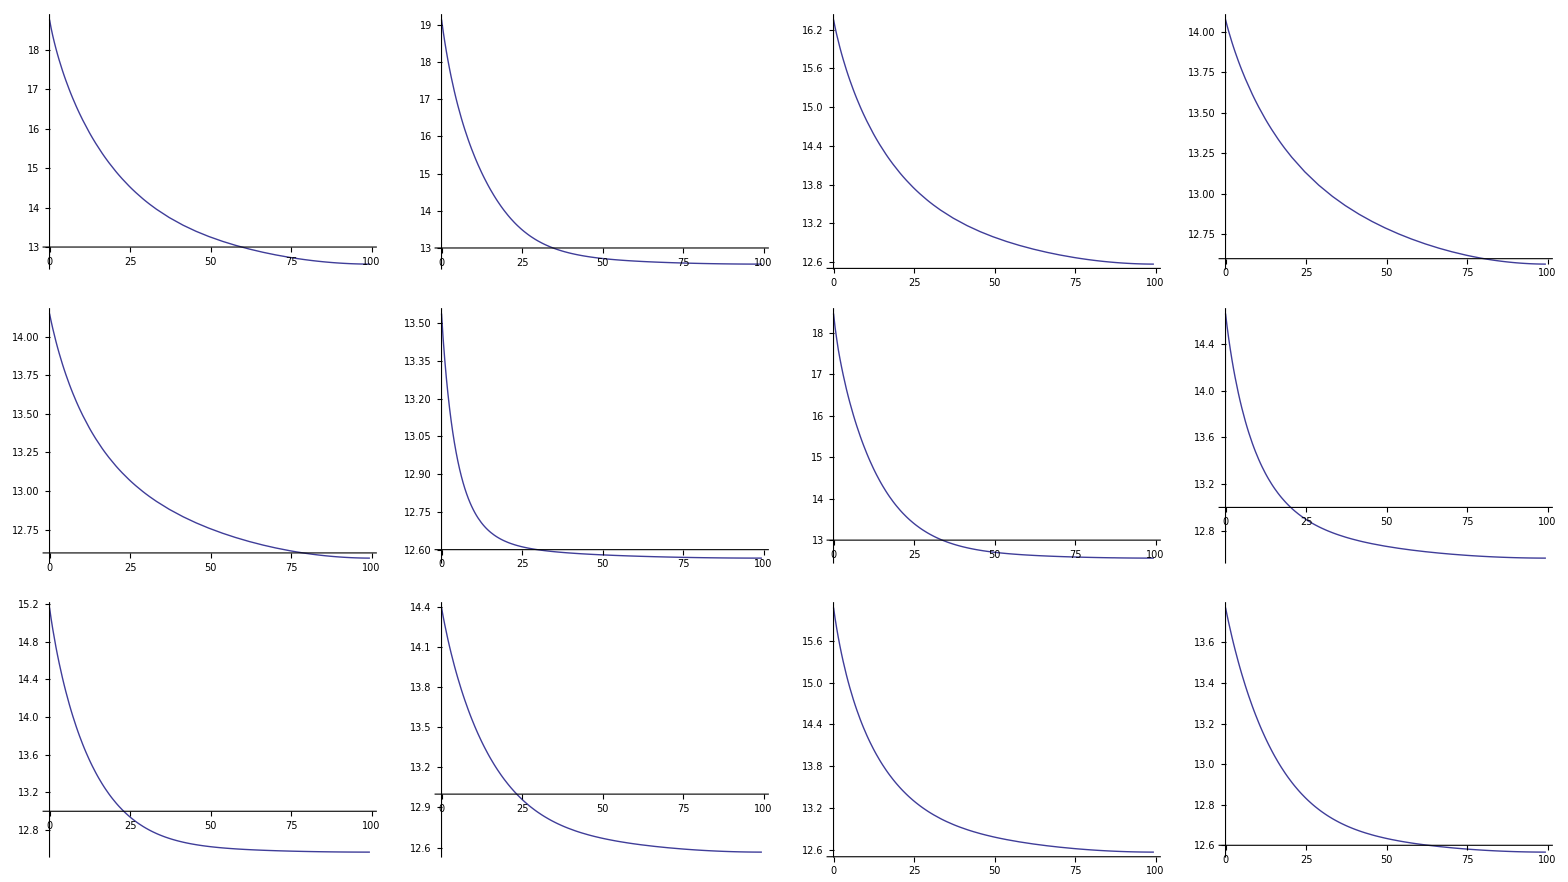

```mathematica
invplots=TableForm[Table[Table[l2a[4j+ i],{i,1,4}],{j,0,2}]]
```

```mathematica
Export["l2a.gif",invplots];
```

#### iso fitting

```mathematica
Do[Subscript[iso, num][t_]=llafit[num,10],{num,{0,43,44}}]
```

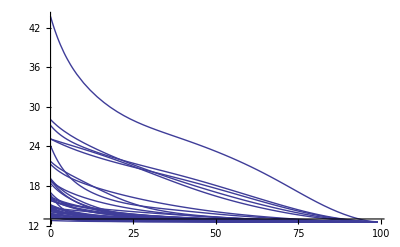

```mathematica
isogra=Show[Table[Plot[Subscript[iso, i][t],{t,0,99},PlotRange->All],{i,1,43}]]
```

```mathematica
Export["isoperimetric_ratio(t).gif",isogra];
```

#### plots for paper

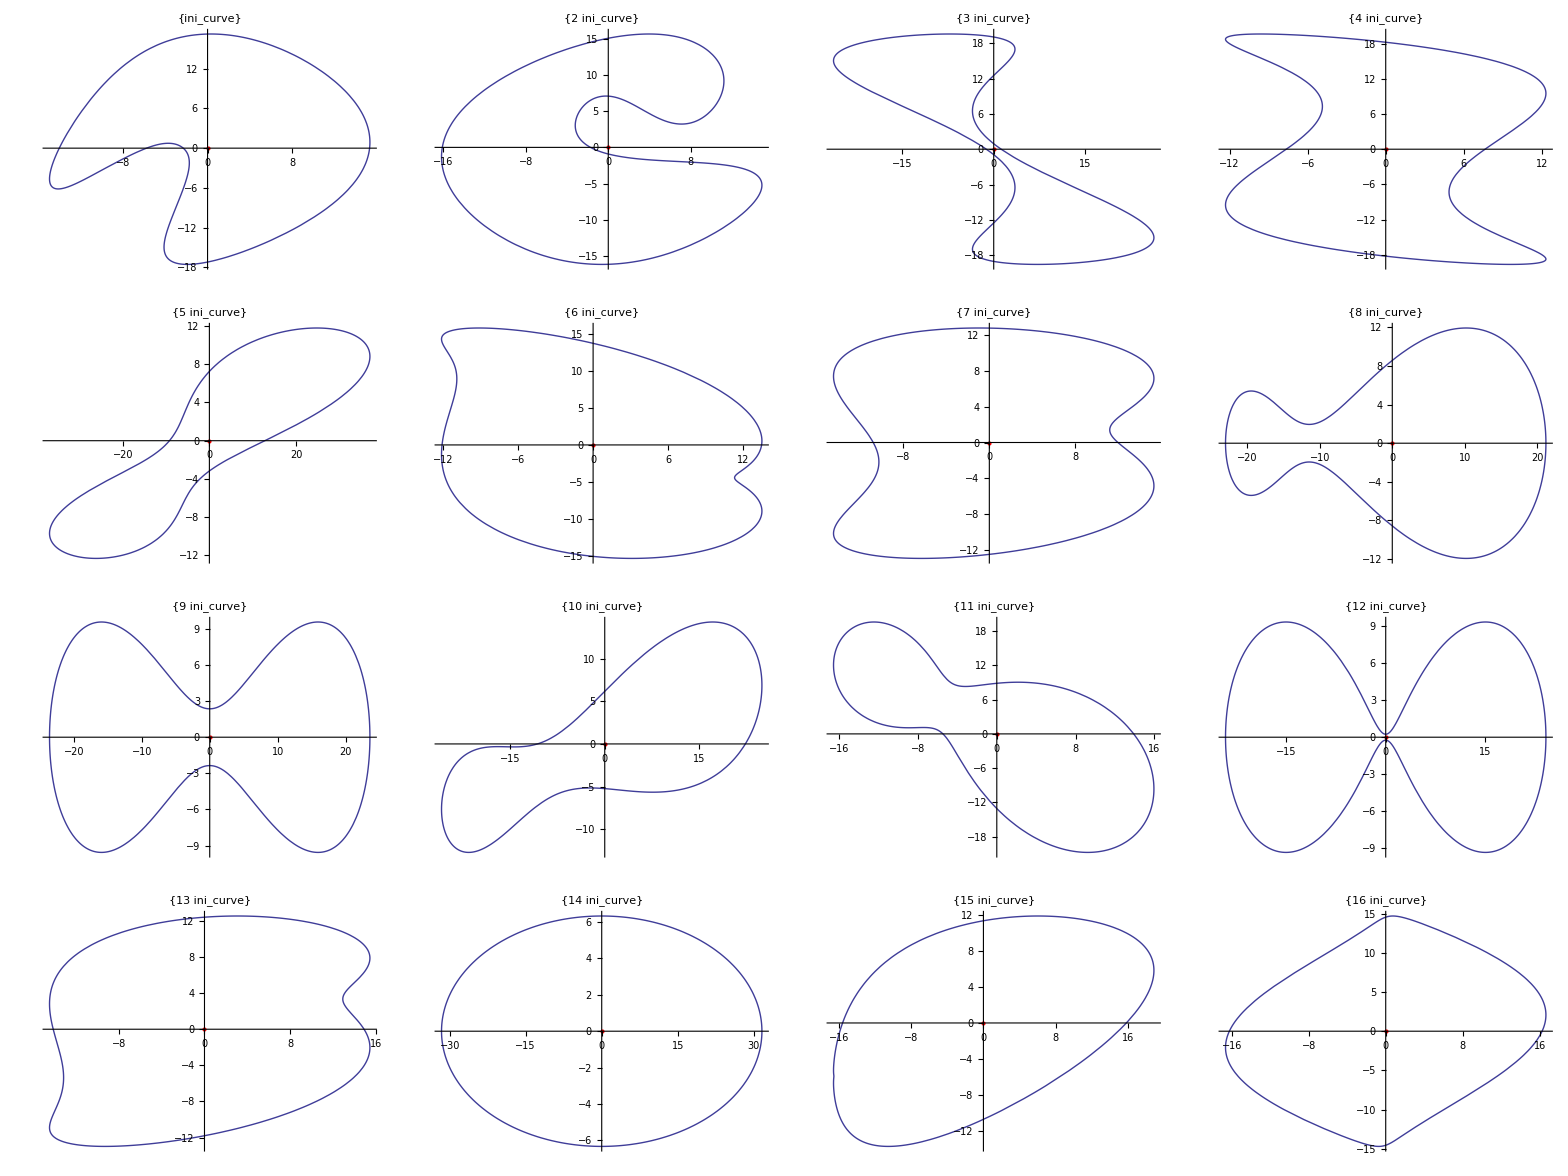

```mathematica
iniplots
```

```mathematica
evo[9,100]
```

```mathematica
evoplot[9,PlotStyle->Black,Boxed->False,BoxRatios->{2,1,2}]
```

-Graphics3D-

```mathematica
evoplot9black=Block[{num=9,step=1,stretch=1,plots,n=Subscript[gpn, num,step],t1=Subscript[tf, num,step-1],t2=Subscript[tf, num,step]},
plots=Table[{stretch Subscript[x, i][t]/.Subscript[sol, num,step][[1,i+1]],stretch Subscript[y, i][t]/.Subscript[sol, num,step][[1,i+n+2]],t},{i,0,n}
];
ParametricPlot3D[{plots//Evaluate},{t,t1,t2},PlotStyle->Black,Boxed->False,BoxRatios->{2,1,2}]
]
```

```mathematica
Export["plot3D_evolution_under_flow.ps",evoplot9black]
```

### partition function

```mathematica
Block[{clist={0},noc,pde,bc,c},
noc=Length[clist];
z[t_]:=Sum[Exp[-Subscript[iso, num][t](1+c[t]/Subscript[l, num][t])],{num,clist}];
pde=Evaluate[D[z[t], t]] ==0;
bc=Sum[Subscript[l, num][t] Exp[-Subscript[iso, num][0](1+c[t]/Subscript[l, num][t])] /.t->0,{num,clist}]/z[0]==Sum[Subscript[l, num][t]/.t->0,{num,clist}]/noc;
Subscript[co, 0]=c[0]/.FindRoot[bc,{c[0],-200}];
Print[{noc,Subscript[co, noc]}];

Timing[Subscript[zsol, 0]=NDSolve[{pde,c[0]==Subscript[co, 0]},c,{t,0,99.9}]]//Print;
]
```

{1,-290.}

{0.008001,{{c→InterpolatingFunction[{{0.,99.9}},<>]}}}

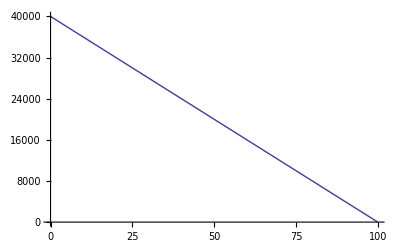

```mathematica
Plot[(c[t]/.Subscript[zsol, 0][[1]])^2,{t,0,99.9},PlotRange->All]
```

```mathematica
Block[{clist={43},noc,pde,bc,c},
noc=Length[clist];
z[t_]:=Sum[Exp[-Subscript[iso, num][t](1+c[t]/Subscript[l, num][t])],{num,clist}];
pde=Evaluate[D[z[t], t]] ==0;
bc=Sum[Subscript[l, num][t] Exp[-Subscript[iso, num][0](1+c[t]/Subscript[l, num][t])] /.t->0,{num,clist}]/z[0]==Sum[Subscript[l, num][t]/.t->0,{num,clist}]/noc;
Subscript[co, noc]=c[0]/.FindRoot[bc,{c[0],-290}];
Print[{noc,Subscript[co, noc]}];

Timing[Subscript[zsol, noc]=NDSolve[{pde,c[0]==Subscript[co, noc]},c,{t,0,99.9}]]//Print;
]
```

{1,-290.}

{0.040003,{{c→InterpolatingFunction[{{0.,99.9}},<>]}}}

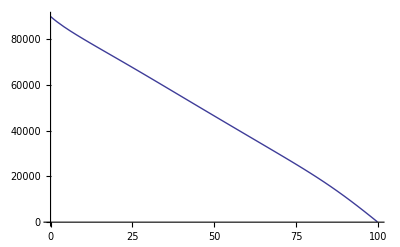

```mathematica
Plot[(c[t]/.Subscript[zsol, 1][[1]])^2,{t,0,99.9},PlotRange->All]
```

```mathematica
Block[{clist={43,44},noc,pde,bc,c},
noc=Length[clist];
z[t_]:=Sum[Exp[-Subscript[iso, num][t](1+c[t]/Subscript[l, num][t])],{num,clist}];
pde=Evaluate[D[z[t], t]] ==0;
bc=Sum[Subscript[l, num][t] Exp[-Subscript[iso, num][0](1+c[t]/Subscript[l, num][t])] /.t->0,{num,clist}]/z[0]==Sum[Subscript[l, num][t]/.t->0,{num,clist}]/noc;
Subscript[co, noc]=c[0]/.FindRoot[bc,{c[0],-290}];
Print[{noc,Subscript[co, noc]}];

Timing[Subscript[zsol, noc]=NDSolve[{pde,c[0]==Subscript[co, noc]},c,{t,0,99.9}]]//Print;
]
```

{2,-325.482}

{36.1343,{{c→InterpolatingFunction[{{0.,99.9}},<>]}}}

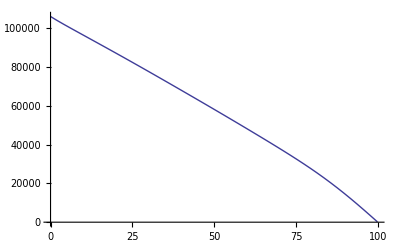

```mathematica
Plot[(c[t]/.Subscript[zsol, 2][[1]])^2,{t,0,99.9},PlotRange->All]
```

```mathematica
Quiet[cgras=TableForm[Table[Table[Plot[c[t]/.Subscript[zsol, 4j+ i][[1]],{t,0,99.9},PlotRange->All,PlotRange->{{0,100},{-221,0}},PlotLabel->"c(t), c(0)="[Subscript[co, 4j+ i]]],{i,1,4}],{j,0,7}]]];
Quiet[ccgras=TableForm[Table[Table[Plot[(c[t]/.Subscript[zsol, 4j+ i][[1]])^2,{t,0,99.9},PlotRange->{{0,100},{0,50000}},PlotLabel->"c(t)^2, c(0)="[Subscript[co, 4j+ i]]],{i,1,4}],{j,0,7}]]];
Export["c(t)_plots,nmax=32.gif", cgras];
Export["c(t)^2_plots,nmax=32.gif", ccgras];
```

```mathematica
Block[{noc=2},
Quiet[vtab=Block[{n=noc},
TableForm[Table[Table[ccfit[i,9.99 j,9.99(j+1)][[2]],{j,0,9}],{i,1,n}],TableHeadings->{Table[i,{i,1,n}],Table[{9.99i,9.99(i+1)},{i,0,9}]}]]];
Quiet[ktab=Block[{n=noc},
TableForm[Table[Table[ccfit[i,9.99 j,9.99(j+1)][[1]],{j,0,9}],{i,1,n}],TableHeadings->{Table[i,{i,1,n}],Table[{9.99i,9.99(i+1)},{i,0,9}]}]]];

Quiet[vtab2=Block[{n=noc},
TableForm[Table[Table[ccfit[i,90+0.99 j,90+0.99(j+1)][[2]],{j,0,9}],{i,1,n}],TableHeadings->{Table[i,{i,1,n}],Table[{90+0.99i,90+0.99(i+1)},{i,0,9}]}]]];
Quiet[ktab2=Block[{n=noc},
TableForm[Table[Table[ccfit[i,90+0.99 j,90+0.99(j+1)][[1]],{j,0,9}],{i,1,n}],TableHeadings->{Table[i,{i,1,n}],Table[{90+0.99i,90+0.99(i+1)},{i,0,9}]}]]];

Export["v-table,[0,100].gif",Labeled[vtab,"v-table, 0 < n < 31, 0 < t < 99.9",Top]];
Export["k-table,[0,100].gif",Labeled[ktab,"k-table, 0 < n < 31, 0 < t < 99.9",Top]];

Export["v-table,[90,100].gif",Labeled[vtab2,"v-table, 0 < n < 31, 90 < t < 99.9",Top]];
Export["k-table,[90,100].gif",Labeled[ktab2,"k-table, 0 < n < 31, 90 < t < 99.9",Top]];
]
```

```mathematica
clgras=TableForm[Table[Table[
lmean[t_]:=Sum[Subscript[l, num][t] Exp[-Subscript[iso, num][t](1+c[t]/Subscript[l, num][t])] ,{num,clist}]/z[t]/. Subscript[zsol, 4j+ i];
Plot[(c[t]/.Subscript[zsol, 4j+ i][[1]])/lmean[t]
,{t,0,99},PlotLabel->"c(t)/<l>(t), c(0)="[Subscript[co, 4j+ i]]],{i,1,4}],{j,0,1}]]
```

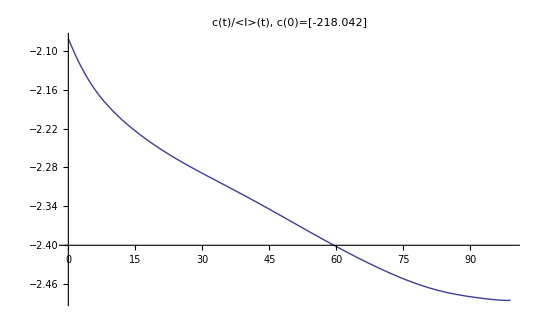

```mathematica
Clear[lmean]; 
lmean[t_]:=Sum[Subscript[l, num][t] Exp[-Subscript[iso, num][t](1+c[t]/Subscript[l, num][t])] ,{num,clist}]/z[t]/. Subscript[zsol, noc];
clgra=Plot[{(c[t]/.Subscript[zsol, noc][[1]])/lmean[t]},{t,0,99},PlotRange->All,PlotLabel->"c(t)/<l>(t), c(0)="[Subscript[co, noc]]]
```

```mathematica
Quiet[zgras=TableForm[Table[Table[zo=Subscript[z, 4j+ i][0]/.Subscript[zsol, 4j+ i][[1]];Plot[(Subscript[z, 4j+ i][t]/.Subscript[zsol, 4j+ i][[1]])/zo,{t,0,99},PlotRange->All,PlotLabel->"z(t)/z(0), c(0)="[Subscript[co, 4j+ i]]],{i,1,4}],{j,0,1}]]];
Export["z(t)z(0)^(-1)_plots,nmax=32.gif", zgras];
```

```mathematica
Import["z(t)z(0)^(-1)_plots,nmax=32.gif"]
```

-Graphics-

### old stuff

#### ndsolve, process equation, iterate, MethodData

```mathematica
ifun=c/.zsol[[1]]
```

InterpolatingFunction[{{0.,99.}},<>]

```mathematica
state=First[NDSolve`ProcessEquations[{pde,c[0]==co},c,t]]
```

NDSolve`StateData[<0.>]

```mathematica
NDSolve`Iterate[state,99.9]
```

```mathematica
zsoll=NDSolve`ProcessSolutions[state]
```

{c→InterpolatingFunction[{{0.,99.9}},<>]}

```mathematica
state@MethodData
```

{None,NDSolve`LSODA[NDSolve`MethodData[3,20,{{_Real,0,7,0,3,20,10,12,5,13,0,-7,0,2,6,6,1,1,{},{{-185.208},{0.487066},{0.000710132},{2.50297×10^-6},{-1.65686×10^-7},{-1.17524×10^-8},{-1.49224×10^-9},{7.9379×10^-216},{1.3166×10^-205},{1.69372×10^-314},{8.16064×10^-255},{1.69372×10^-314},{-0.0000137429}},{0.,0.,0.000471104,10.,0.,9.51879,0.00296791,0.00296791,0.48121,0.48121,0.48121,0.}},False,12,{NDSolve`Newton,{Automatic}},None,False}]]}

```mathematica
Do[Subscript[iso, i][t]>>>"isofunc",{i,4,43}]
```

#### equidistant u-values & discrte controid computation

```mathematica
Module[{fitpts=100,l,L,usol,uvalues,centroid},
l[i_]:=length i/fitpts;
L[u_?NumberQ]:=
NIntegrate[Sqrt[Evaluate[(D[initialcurve[p], p]).(D[initialcurve[p], p])]],{p,0,u},MaxRecursion->20];
usol[i_]:=FindRoot[L[u]==l[i],{u,0,2Pi}];
uvalues=Table[usol[i],{i,0,fitpts-1}];
centroid=1/Length[uvalues] Total[initialcurve[u]/.uvalues]
];
```